```mathematica
$Assumptions = x1 ∈Reals&& x2∈Reals&&x3∈Reals&&x4 ∈Reals&& s∈Reals;
ϕ[x1_,x2_,s_] = x1^2 + (x2 - s)^2;
```

```mathematica
Dϕ = D[ϕ[x1,x2,s],{{x1,x2}}];
Dϕinverse=Dϕ/Norm[Dϕ]^2//FullSimplify ;
```

```mathematica
ϕ' = (D[ϕ[x1,x2,s[t]],t])/.{s'[t] -> s', s[t]->s};
ϕ'' = (D[ϕ[x1,x2,s[t]],{t,2}])/.{s'[t] -> s', s[t]->s};
```

```mathematica
v = Simplify[- Dϕinverse ϕ',x1^2 + (x2 - s)^2==1]/.{s'->p};
v = v/.{s->x2-Sqrt[1-x1^2]};
Solve[v[[1]]^2+v[[2]]^2==1&&0<=x1<1,p]//Simplify
```

{{p→ConditionalExpression[-1/(√(1-x1^2)), 0<x1<1]},{p→ConditionalExpression[1/(√(1-x1^2)), 0<x1<1]}}

```mathematica
v/.{p->1/Sqrt[1-x1^2]}//Simplify
```

{x1,√(1-x1^2)}

```mathematica
sols = Insert[Table[
DSolve[x1'[t] == x1[t]&&x2'[t]==√(1-x1[t]^2)&&x1[0]==Cos[θ]&&x2[0]==Sin[θ],{x1[t],x2[t]},t][[1]],{θ,0,Pi,Pi/100}],{x1[t]->0,x2[t]->1+t},50];
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

Part::partw: Part 1 of {} does not exist.

```mathematica
DSolve[x1'[t] == x1[t]&&x2'[t]==√(1-x1[t]^2)&&x1[0]==Cos[θ]&&x2[0]==Sin[θ],{x1[t],x2[t]},t][[1]];
{x1,x2}={x1[t],x2[t]}/.%;
zcurves = Table[
ParametricPlot[
{x1,x2}/.{t->τ},
{θ,0,Pi},
PlotRange->{{-1,1},{0,1.5}},
PlotStyle->Black
],{τ,-.5,.5,.25}];
ClearAll[x1,x2];
```

```mathematica
DSolve[x1'[t] == x1[t]&&x2'[t]==√(1-x1[t]^2)&&x1[0]==Cos[θ]&&x2[0]==Sin[θ],{x1[t],x2[t]},t][[1]];
{x1,x2}={x1[t],x2[t]}/.%;
f = Table[
ParametricPlot[
{x1,x2}/.{t->τ},
{θ,0,Pi},
PlotRange->{{-1,1},{0,1.5}},
PlotStyle->Black
],{τ,-.5,.5,.05}];
ClearAll[x1,x2];
```

```mathematica
refcurve = ListLinePlot[
Table[{x1[t],x2[t]}/.sols[[n]]/.{t->0},{n,1,Length[sols]}],PlotStyle->Red
];
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

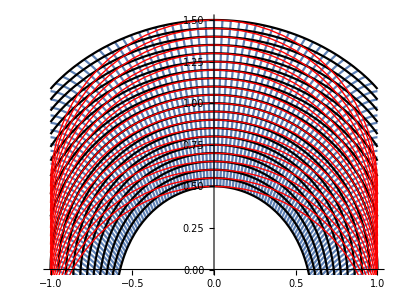

```mathematica
Show[
Table[
ParametricPlot[
{x1[t],x2[t]}/.sols[[n]],{t,-.5,.5},
Background->White,
PlotRange->{{-1,1},{0,1.5}}
],
{n,1,Length[sols]}
],
f,
Table[Graphics[{Red,Circle[{0,n},1,{0,Pi}]}],{n,-.5,.5,.05}]
]
```

```mathematica
(*k = Table[
D[{x1[t],x2[t]}/.sols[[n]],{t,2}],{n,1,Length[sols]}]/.{t->0}//N;*)
```

### Normal family and translates of the manifold

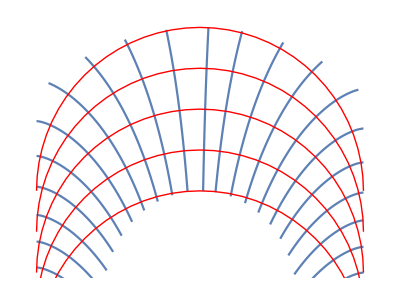

```mathematica
Show[Table[
ParametricPlot[
{x1[t],x2[t]}/.sols[[n]],{t,-.5,.5},
Background->White,
PlotRange->{{-1,1},{0,1.5}}
],
{n,1,Length[sols],5}
], 
Table[Graphics[{Red,Circle[{0,n},1,{0,Pi}]}],{n,-.5,.5,.25}],
Axes->False
]
```

### The normal family of curves and the curves z = const

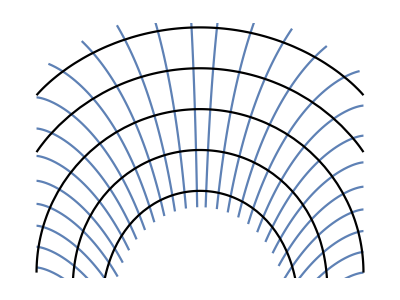

```mathematica
Show[Table[
ParametricPlot[
{x1[t],x2[t]}/.sols[[n]],{t,-.6,.6},
Background->White,
PlotRange->{{-1,1},{0,1.5}}
],
{n,1,Length[sols],4}
], 
zcurves,
Axes->False
]
```

### Curves z = const and translates of the manifold

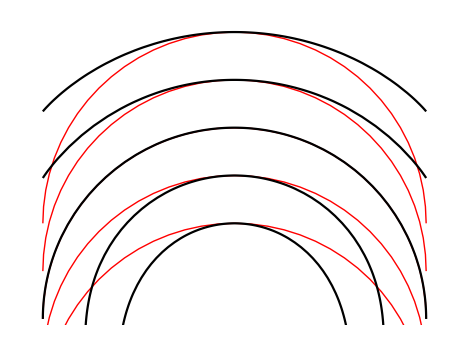

```mathematica
Show[
Table[Graphics[{Red,Circle[{0,n},1,{0,Pi}]}],{n,-.5,.5,.25}],
zcurves,
PlotRange->{{-1,1},{0,1.5}},
Background->White
]
```